#### Design of a controller for a Modelica Model from Wolfram SystemModeler

```mathematica
SystemModel;WSM`$WSMVersion
```

12.0.0 (build ID 1699, installer build ID 12.0.0.2966-CI) created on Fri 14 Sep 2018 08:16:58

Define the model

```mathematica
model = "Conference2018.ElevatorModel"
```

Conference2018.ElevatorModel

```mathematica
sm = SystemModel[model]
```

-Graphics-

Simulate the model to Steady State and grab the model from WSM

```mathematica
sim =SystemModelSimulate[model,All,500,Method->{"StopAtSteadyState"->True}]
```

SystemModelSimulate::rss: Simulation reached steady state.

SystemModelSimulationData[…]

```mathematica
lsm=WSM`LocalizedSystemModel[sim,"StopTime"]
```

WSM`SystemModelEquations[<|Localized -> True, Model -> Conference2018.ElevatorModel, Equations -> {0 == WSMLink`DotName[prismatic1, frame_a, f[1]][t] + WSMLink`DotName[prismatic1, frame_b, f[1]][t], 0 == <<1>>, 0 == <<1>>, <<1865>>, WSMLink`DotName[world, z_label, cylinders[3], R, w[3]][t] == WSMLink`DotName[world, z_label, R, w[3]][t]}, <<20>>, Unsupported -> {}|>]

```mathematica
lsm["Properties"]
```

{AlgebraicEquations,Balanced,DifferentialEquations,DiscreteVariables,DisplayEquations,DisplayEventEquations,DisplayOutputExpressions,DisplayRemovedVariables,Equations,EvaluateParameters,EventEquations,Inputs,Linearization,Localized,Model,NumberOfEquations,NumberOfVariables,OperatingPoint,OutputExpressions,Outputs,Parameters,ParameterValues,RemovedVariables,SelectedOutputs,SelectOutputs,Simplify,Summary,Variables}

Now get the simplified Equations

```mathematica
simp = lsm["SelectOutputs",{"HeightOut"}]
```

WSM`SystemModelEquations[<|Localized -> True, Model -> Conference2018.ElevatorModel, Equations -> {0 == WSMLink`DotName[prismatic1, frame_a, f[1]][t] + WSMLink`DotName[prismatic1, frame_b, f[1]][t], 0 == <<1>>, 0 == <<1>>, <<1865>>, WSMLink`DotName[world, z_label, cylinders[3], R, w[3]][t] == WSMLink`DotName[world, z_label, R, w[3]][t]}, <<20>>, Unsupported -> {}|>]

```mathematica
simp2 = simp["Simplify"]
```

WSM`SystemModelEquations[<|Localized -> True, Model -> Conference2018.ElevatorModel, Equations -> {WSMLink`DotName[position1, v][t] == (WSMLink`DotName[prismatic2, s])'[t], WSM<<9>>ame[<<2>>][t] == <<3>>'[t], <<3>>, WSMLink`DotName[HeightOut][t] == 2. + WSMLink`DotName[prismatic2, s][t] + WSMLink`DotName[springDamper1, s_rel][t]}, <<21>>, AllFunctionsInlined -> True|>]

```mathematica
simp2["Properties"]
```

{AlgebraicEquations,Balanced,DifferentialEquations,DiscreteVariables,DisplayEquations,DisplayEventEquations,DisplayOutputExpressions,DisplayRemovedVariables,Equations,EvaluateParameters,EventEquations,Inputs,Linearization,Localized,Model,NumberOfEquations,NumberOfVariables,OperatingPoint,OutputExpressions,Outputs,Parameters,ParameterValues,RemovedVariables,SelectedOutputs,SelectOutputs,Simplify,Summary,Variables}

Examine the Equations, Operating Point and Parameters

```mathematica
simp2["DisplayEquations"]
```

Differential equations
position1.v Speed==prismatic2.s Length'
body1.v_0[2] Speed==HeightOut '
position1.v Speed'==10.167 position1.f_crit Frequency (-1.3617 position1.v Speed+6.28319 (-prismatic2.s Length+position ) position1.f_crit Frequency)
-9.81-body1.v_0[2] Speed'==springDamper1.f_c Force+0.1 springDamper1.s_rel Length'
Algebraic equations
HeightOut ==2.+prismatic2.s Length+springDamper1.s_rel Length
springDamper1.f_c Force==40 (2+springDamper1.s_rel Length)

```mathematica
initialCond =simp2["OperatingPoint"];
parameterVals = simp2["ParameterValues"];
```

Insert Parameter Values

```mathematica
simp2["DisplayEquations"]/. parameterVals
```

Differential equations
position1.v Speed==prismatic2.s Length'
body1.v_0[2] Speed==HeightOut '
position1.v Speed'==10.167 50 (-1.3617 position1.v Speed+6.28319 50 (-prismatic2.s Length+position ))
-9.81-body1.v_0[2] Speed'==springDamper1.f_c Force+0.1 springDamper1.s_rel Length'
Algebraic equations
HeightOut ==2.+prismatic2.s Length+springDamper1.s_rel Length
springDamper1.f_c Force==40 (2+springDamper1.s_rel Length)

```mathematica
equations = simp2["Equations"]
```

{position1.v Speed[t]==prismatic2.s Length'[t],body1.v_0[2] Speed[t]==HeightOut '[t],position1.v Speed'[t]==10.167 position1.f_crit Frequency (-1.3617 position1.v Speed[t]+6.28319 position1.f_crit Frequency (position [t]-prismatic2.s Length[t])),-9.81-body1.v_0[2] Speed'[t]==springDamper1.f_c Force[t]+0.1 springDamper1.s_rel Length'[t],springDamper1.f_c Force[t]==40 (2+springDamper1.s_rel Length[t]),HeightOut [t]==2.+prismatic2.s Length[t]+springDamper1.s_rel Length[t]}

```mathematica
vars = simp2["Variables"]
```

{HeightOut ,body1.v_0[2] Speed,position1.v Speed,prismatic2.s Length,springDamper1.f_c Force,springDamper1.s_rel Length}

```mathematica
inputvars = simp2["Inputs"]
```

{position }

```mathematica
outputvars = simp2["Outputs"]
```

{HeightOut }

## LQG Servo Design Demo

### Descriptor State Space System Model of Elevator

```mathematica
demoSysDescriptor = simp2["Linearization"]/. parameterVals
```

000100001000010000001000000.0.-1.0.0.0.0.0.692.218159702.0.0.-159702.0.1.0.0.0.0.10.0.0.0.-1.0.0.00000000001-400000000100-10-101000000positionHeightOutHeightOutbody1.v_0[2]position1.vprismatic2.sspringDamper1.f_cspringDamper1.s_relStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6positionHeightOutHeightOutbody1.v_0[2]position1.vprismatic2.sspringDamper1.f_cspringDamper1.s_relIdentityAutomatic11611121313233343536TrueTrueTrueAutomaticpositionHeightOutHeightOutbody1.v_0[2]position1.vprismatic2.sspringDamper1.f_cspringDamper1.s_relAutomatic

### Transform the demo model from descriptor form to regular state-space:

```mathematica
demoSys=
StateSpaceModel[
demoSysDescriptor,
StateSpaceRealization->"ControllableCompanion"]
```

01.0.0.000.1.0.000.0.1.0-6.38809×10^6-43659.-159812.-692.3181.6.38809×10^615970.2000positionHeightOutHeightOutbody1.v_0[2]position1.vprismatic2.sStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4positionHeightOutHeightOutbody1.v_0[2]position1.vprismatic2.sIdentityAutomatic1141112131323334TrueTrueFalseAutomaticpositionHeightOutHeightOutbody1.v_0[2]position1.vprismatic2.sspringDamper1.f_cspringDamper1.s_relAutomatic

Create and merge an Integrator into the system

### Add a second input identical to the first; one for u-feedback, one for u-w for compatibility with LQGRegulator[ ] convention.

```mathematica
sumDualIn=StateSpaceModel[{{{}},{{}},{{}},{{1,1}}}]
demoSys2In=SystemsModelSeriesConnect[sumDualIn,demoSys]
```

11StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2101FalseFalseFalseAutomaticNoneAutomatic

01.0.0.0.0.00.1.0.0.0.00.0.1.0.0.-6.38809×10^6-43659.-159812.-692.3181.1.6.38809×10^615970.20000HeightOutStateSpaceModelFalseTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$HeightOutControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic214121FalseTrueFalseAutomaticNoneHeightOutAutomatic

### Create a state space model of a simple integrator with a single input, and no output. A slight bit of damping added

```mathematica
intUo = StateSpaceModel[{{{-0.0001}},{{1}},{{}},{{}}}]
```

-0.00011StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Identity1011FalseFalseFalseAutomaticNoneAutomatic

### Merge the integrator (intUo) into the demo system (demoSys2In)

```mathematica
demoSysUo=SystemsModelMerge[{intUo,demoSys2In}]
```

-0.00010000100001.0.0.00.0.000.1.0.00.0.000.0.1.00.0.0-6.38809×10^6-43659.-159812.-692.31801.1.06.38809×10^615970.200000HeightOutStateSpaceModelFalseTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$HeightOutControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic315121FalseTrueFalseAutomaticNoneHeightOutAutomatic

Connect the feedback to the integrator, Next design the LQG Regulator

### Add feedback from the output of the simple system to the input of the integrator. The regulator will try to zero this first input by adjusting the feedback position. Use a plus sign on the feedback so the regulated system will travel in the desired direction.

```mathematica
demoSysUoFb=SystemsModelFeedbackConnect[demoSysUo,{{1,1,1}}]
```

-0.00016.38809×10^615970.20.0.1.0.0.0.0.1.0.0.0.0.0.0.0.0.1.0.0.0.0.0.0.0.0.1.0.0.0.0.-6.38809×10^6-43659.-159812.-692.3180.1.1.0.6.38809×10^615970.20.0.0.0.0.HeightOutStateSpaceModelFalseTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$HeightOutControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic315121FalseTrueFalseAutomaticNoneHeightOutAutomatic

### Generate an LQG regulator for compSysUoFb, note that the first input will be our servo reference.

```mathematica
demoSysUoFbReg=
LQGRegulator[
{demoSysUoFb,1,2,1},
{{{1}},{{0.001}}},
{DiagonalMatrix[{10,1,1,1,1}],{{.01}}}]
```

-0.0001201908.504.7690.0.1.0.9683930.-46.36260.8840940.0.0.7.25766×10^-60.-1215.71-3.039271.0.0.0.0001903090.-1825.14-4.562860.1.0.0.00028571-31.6222-3.50113×10^7-3.21592×10^6-173202.-711.4660.-0.173731.62222.97328×10^73.17504×10^613390.119.14830.0.HeightOutStateSpaceModelTrueFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$HeightOutControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic215112TrueFalseFalseAutomaticNoneHeightOutNoneAutomatic

Now we can test the new regulator by simulating it in Mathematica, First Connect the regulator and the system

### Cascade the regulator simpSysUoFbReg with the un-modified (not simpSysUo) simple system, connecting the output of the regulator (port 1) to the input of simpSys (port 1)

```mathematica
demoSysUoFbRegDemoSys=SystemsModelSeriesConnect[demoSysUoFbReg,demoSys,{{1,1}}]
```

-0.0001201908.504.7690.0.00001.0.9683930.-46.36260.8840940.0.00000.7.25766×10^-60.-1215.71-3.039271.0.00000.0.0001903090.-1825.14-4.562860.1.00000.0.00028571-31.6222-3.50113×10^7-3.21592×10^6-173202.-711.46600000.-0.17370.0.0.0.0.01.0.0.0.0.0.0.0.0.0.00.1.0.0.0.0.0.0.0.0.00.0.1.0.0.31.62222.97328×10^73.17504×10^613390.119.1483-6.38809×10^6-43659.-159812.-692.3180.0.0.0.0.0.0.6.38809×10^615970.2000.0.HeightOutHeightOutStateSpaceModelTrueTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8$CellContext`stname9Control`CommonDump`$DUMMY$HeightOutHeightOutControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic21911221TrueTrueFalseAutomaticNoneHeightOutHeightOutAutomatic

### Hook the output of the serial combined system (port 1) simpSysUoFbRegSimpSys to the regulator sensor input (port 2)

```mathematica
demoSysServ=SystemsModelFeedbackConnect[demoSysUoFbRegDemoSys,{1,2,-1}]
```

-0.0001201908.504.7690.0.-6.18619×10^6-15465.50.0.1.0.9683930.-46.36260.8840940.0.-46.3626-0.1159060.0.0.7.25766×10^-60.-1215.71-3.039271.0.-1215.71-3.039270.0.0.0.0001903090.-1825.14-4.562860.1.-1825.14-4.562860.0.0.0.00028571-31.6222-3.50113×10^7-3.21592×10^6-173202.-711.4661.10962×10^62774.040.0.0.-0.17370.0.0.0.0.0.1.0.0.0.0.0.0.0.0.0.0.0.1.0.0.0.0.0.0.0.0.0.0.0.1.0.0.31.62222.97328×10^73.17504×10^613390.119.1483-6.38809×10^6-43659.-159812.-692.3180.0.0.0.0.0.0.6.38809×10^615970.20.0.0.0.HeightOutHeightOutStateSpaceModelTrueTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8$CellContext`stname9Control`CommonDump`$DUMMY$HeightOutHeightOutControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic21911221TrueTrueFalseAutomaticNoneHeightOutHeightOutAutomatic

Simulate and plot the response

### Original open-loop system and closed-loop LQG servo system

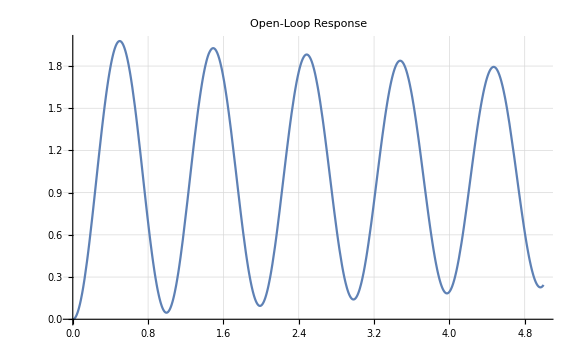
EigenValues:
-346.109-199.777 ⅈ
-346.109+199.777 ⅈ
-0.05-6.32436 ⅈ
-0.05+6.32436 ⅈ | -Graphics-

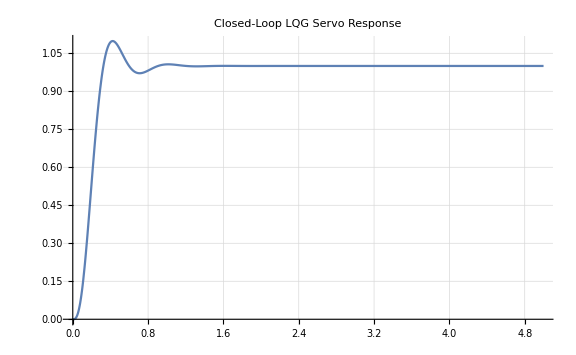
EigenValues:
-346.145-199.715 ⅈ
-346.145+199.715 ⅈ
-346.105-199.771 ⅈ
-346.105+199.771 ⅈ
-24.7545-25.5499 ⅈ
-24.7545+25.5499 ⅈ
-9.588+0. ⅈ
-4.79407-10.4376 ⅈ
-4.79407+10.4376 ⅈ | -Graphics-

```mathematica
tmaxDemo=5;
demoSysOut=OutputResponse[demoSys2In,{1,0}*UnitStep[t],{t,0,tmaxDemo}];
demoSysServOut = OutputResponse[demoSysServ,{1,0}*UnitStep[t],{t,0,tmaxDemo}];
Grid[{{Prepend[Sort[Eigenvalues[Normal[demoSys][[1]]]],"   EigenValues:"]//TableForm,Plot[demoSysOut,{t,0,tmaxDemo},GridLines->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"Open-Loop Response"]}}]
Grid[{{Prepend[Sort[Eigenvalues[Normal[demoSysServ][[1]]]],"   EigenValues:"]//TableForm,Plot[demoSysServOut,{t,0,tmaxDemo},PlotRange->All,GridLines->Automatic,ImageSize->Large,PlotLabel->"Closed-Loop LQG Servo Response"]}}]
```

#### Load the regulator into WSM

```mathematica
regmodel=CreateSystemModel["Conference2018.Regulator",demoSysUoFbReg];
```